Exlusion probability

```mathematica
Pr[m_,n_,N_,b_,ξ_,r_]:= Erf[(Surd[ (N*ξ),4]*r)/(b*Sqrt[2*(1-Exp[-Abs[m-n]*Sqrt[N*ξ]])])]
```

```mathematica
Pr[m,n,N,ξ,r]
```

Pr[m,n,N,ξ,r]

```mathematica
Manipulate[Plot3D[Pr[m,n,N,b,(2*Nc)/((N-1)*(N-2)),r],{Nc,0,100},{r,0,0.2},AxesLabel->{Nc,r,Pr}],{b,0.2},{N,100},{m,1,100,1},{n,1,100,1}]
```

N$$::shdw: Symbol "N$$" appears in multiple contexts {"System`", "Global`"}; definitions in context "System`" may shadow or be shadowed by other definitions.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power :: infy will be suppressed during this calculation.

RCL Polymer Average Volume Exclusion Laplacian Matrix

For undiscriminate exclusion:

```mathematica
VEoff[N_,b_,Nc_,r_]:=SparseArray[{m_,n_}/;m!=n->-Pr[m,n,N,b,(2*Nc)/((N-1)*(N-2)),r],{N,N}]
```

```mathematica
VE[N_,b_,Nc_,r_]:=VEoff[N,b,Nc,r]-DiagonalMatrix[Total[VEoff[N,b,Nc,r],{2}]]
```

```mathematica
Manipulate[MatrixPlot[VE[N,b,Nc,r], PlotLegends->Automatic],{Nc,0,100,1},{N,100},{b,0.2},{r,0,0.3}]
```

MatrixPlot::mat0: Argument VE[N$$, 0.2, 10, 0.0555] at position 1 is not a matrix.

When selective exclusion (repair sphere) is imposed:

```mathematica
ℓ[N_,g_]:=N-g-3
𝒸[m_,N_,g_]:=Piecewise[{{4,Abs[m-(N+1)/2]≤(N-1)/2-g-3},{3,Abs[m-(N+1)/2]==(N-1)/2-g-2},{2,Abs[m-(N+1)/2]≤ (N-1)/2-1},{1,Abs[m-(N+1)/2]==(N-1)/2}}]
beBrokenProbability[m_,n_,N_,g_]:=1/ℓ[N,g]^2*(ℓ[N,g]*(𝒸[m,N,g]+𝒸[n,N,g])-2*𝒸[m,N,g]*𝒸[n,N,g])

SelectivePr[m_,n_,N_,b_,ξ_,r_,g_]:= Erf[(Surd[ (N*ξ),4]*r)/(b*Sqrt[2*(1-Exp[-Abs[m-n]*Sqrt[N*ξ]])])]*beBrokenProbability[m,n,N,g]
```

```mathematica
∑_(m=1)^56 𝒸[m,56,8]
```

180

```mathematica
180
```

```mathematica
∑_(m=1)^100 𝒸[m,100,3]/ℓ[100,3]
```

4

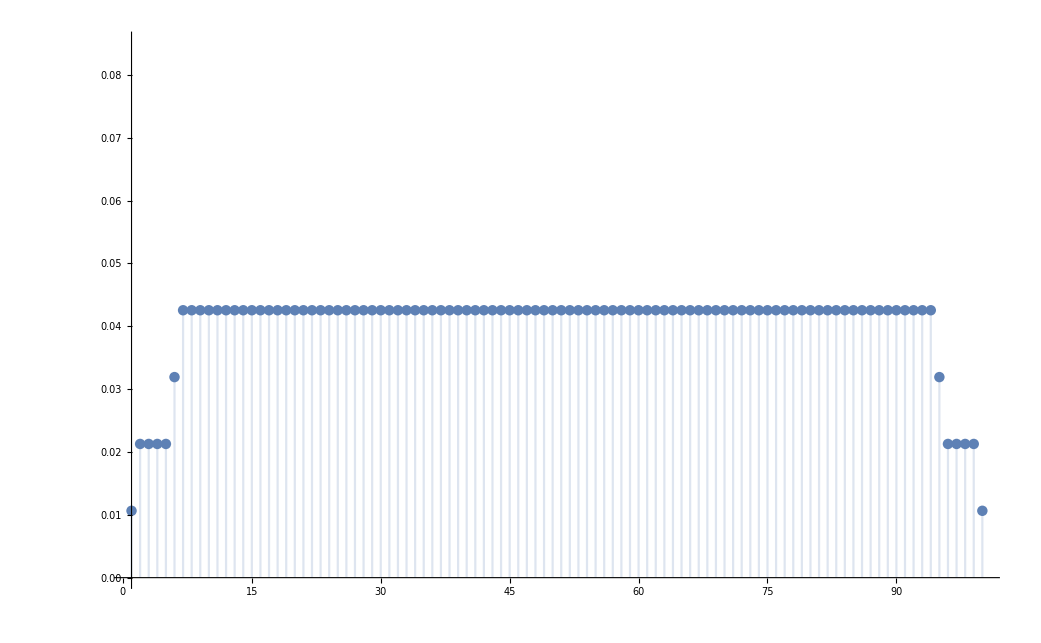

```mathematica
DiscretePlot[𝒸[m,100,3]/ℓ[100,3],{m,1,100}]
```

```mathematica
selectiveVEoff[N_,b_,Nc_,r_,g_]:=SparseArray[{m_,n_}/;m!=n->-SelectivePr[m,n,N,b,(2*Nc)/((N-1)*(N-2)),r,g],{N,N}]
selectiveVE[N_,b_,Nc_,r_,g_]:=selectiveVEoff[N,b,Nc,r,g]-DiagonalMatrix[Total[selectiveVEoff[N,b,Nc,r,g],{2}]]
Manipulate[MatrixPlot[selectiveVE[N,b,Nc,r,g], PlotLegends->Automatic],{Nc,1,100,1},{N,100},{b,0.2},{r,0,0.3},{g,2,50}]
```

MatrixPlot::mat0: Argument selectiveVE[N$$, 0.2, 6, 0.2905, 7.] at position 1 is not a matrix.

```mathematica
Manipulate[ListPlot3D[selectiveVE[N,b,Nc,r,g], PlotRange->Full],{Nc,1,100,1},{N,100},{b,0.2},{r,0,0.3},{g,2,50}]
```

ListPlot3D::arrayerr: selectiveVE[N$$, 0.2, 6., 0.1, 20.] must be a valid array or a list of valid arrays.

Trying to diagonalize:

```mathematica
v[p_,n_,N_]:=If[p==0,√1/N,√2/N Cos[(n-1/2)(p*π)/N]]
V[N_]:=Table[v[p,n,N],{p,0,N-1},{n,N}]
```

```mathematica
MatrixForm[N[V[10].Transpose[V[10]]]]
```

(1. | 0. | 0. | 0. | -5.55112×10^-17 | 0. | 0. | 0. | 5.55112×10^-17 | 0.
0. | 1. | 0. | 5.55112×10^-17 | 0. | 0. | 0. | -5.55112×10^-17 | 0. | 5.55112×10^-17
0. | 0. | 1. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 5.55112×10^-17 | 0. | 1. | 0. | 0. | 0. | -5.55112×10^-17 | 0. | 5.55112×10^-17
-5.55112×10^-17 | 0. | 0. | 0. | 1. | 0. | 0. | 0. | 5.55112×10^-17 | 0.
0. | 0. | 0. | 0. | 0. | 1. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 1. | 0. | 0. | 0.
0. | -5.55112×10^-17 | 0. | -5.55112×10^-17 | 0. | 0. | 0. | 1. | 0. | -5.55112×10^-17
5.55112×10^-17 | 0. | 0. | 0. | 5.55112×10^-17 | 0. | 0. | 0. | 1. | 0.
0. | 5.55112×10^-17 | 0. | 5.55112×10^-17 | 0. | 0. | 0. | -5.55112×10^-17 | 0. | 1.)

```mathematica
ListPlot3D[V[100].selectiveVE[100,0.2,10,0.1,20].Transpose[V[100]],PlotRange->Full]
```

-Graphics3D-

```mathematica
diagVE[N_,b_,Nc_,r_,g_]:=V[N].selectiveVE[N,b,Nc,r,g].Transpose[V[N]]
```

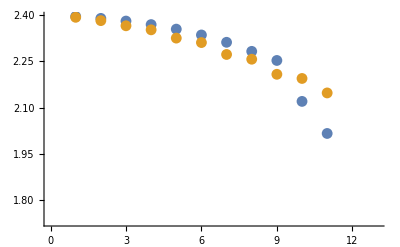

```mathematica
ListPlot[{Eigenvalues[selectiveVE[12,0.2,5,0.1,4]],Reverse[Sort[Diagonal[diagVE[12,0.2,5,0.1,4]]]]}]
```

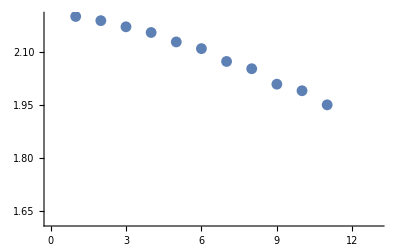

```mathematica
ListPlot[Reverse[Sort[Diagonal[diagVE[12,0.2,5,0.1,4]]]]]
```

##### MEAN BREAK LAPLACIAN MATRIX

```mathematica
Xoff[N_,g_]:= SparseArray[{{i_,j_}:>-𝒸[i,N,g]/;Abs[i-j]==1},{N,N}]
X[N_,g_]:=1/(N-g-3)*(Xoff[N,g]-DiagonalMatrix[Total[Xoff[N,g],{2}]])
```

```mathematica
MatrixForm[X[30,4]]
```

(1/23 | -1/23 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-2/23 | 4/23 | -2/23 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -2/23 | 4/23 | -2/23 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -2/23 | 4/23 | -2/23 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -2/23 | 4/23 | -2/23 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -2/23 | 4/23 | -2/23 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -3/23 | 6/23 | -3/23 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -4/23 | 8/23 | -4/23 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -4/23 | 8/23 | -4/23 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -4/23 | 8/23 | -4/23 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -4/23 | 8/23 | -4/23 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -4/23 | 8/23 | -4/23 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -4/23 | 8/23 | -4/23 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -4/23 | 8/23 | -4/23 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -4/23 | 8/23 | -4/23 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -4/23 | 8/23 | -4/23 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -4/23 | 8/23 | -4/23 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -4/23 | 8/23 | -4/23 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -4/23 | 8/23 | -4/23 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -4/23 | 8/23 | -4/23 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -4/23 | 8/23 | -4/23 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -4/23 | 8/23 | -4/23 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -4/23 | 8/23 | -4/23 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -3/23 | 6/23 | -3/23 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -2/23 | 4/23 | -2/23 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -2/23 | 4/23 | -2/23 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -2/23 | 4/23 | -2/23 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -2/23 | 4/23 | -2/23 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -2/23 | 4/23 | -2/23
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/23 | 1/23)

```mathematica
ListPlot3D[V[50].X[50,10].Transpose[V[50]],PlotRange->Full]
```

-Graphics3D-

```mathematica
diagX[N_,g_]:=V[N].X[N,g].Transpose[V[N]]
```

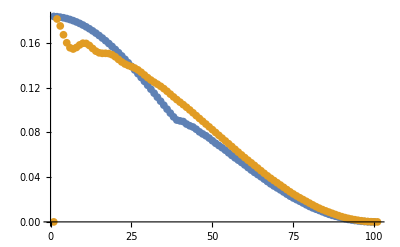

```mathematica
ListPlot[{Eigenvalues[X[100,10]],Reverse[Diagonal[diagX[100,10]]]}]
```

```mathematica
Eigenvalues[X[100,10]]
```

{Root[77371252455336267181195264-3179697347937283821245388816384 #1+72+3153852484851485139368812764771111574230474968783629814617457851044102482909874106933486212373083 #1^50&,50],Root[1&,49],Root[1&,49],Root[1&,48],1,91,Root[1&,2],Root[1&,1],Root[1&,1],0}
 |  |  |  |

```mathematica
MatrixForm[diagX[10,2]]
```

(1)
 |  |  |  |

```mathematica
Dg[N_,g_]:=SparseArray[{{i_,j_}:>𝒸[i,N,g]/;i==j},{N,N}]
```

```mathematica
Dg[20,3] // MatrixForm
```

(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 4 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 4 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 3 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1)

```mathematica
TrigReduce[V[10].Dg[10,3].Transpose[V[10]]] // MatrixForm
```

(9/5 | 0 | -1/5 √(2 (5/8+(√5)/8)) | 0 | -(2 √2)/5+1/5 √2 (1-√5)+(3 (1+√5))/(10 √2) | 0 | -1/5 √(2 (5/8-(√5)/8)) | 0 | (2 √2)/5+1/5 √2 (-1-√5)+(3 (-1+√5))/(10 √2) | 0
0 | 1/20 (36-√(2 (5+√5))) | 0 | 1/20 (-1-√5-√(2 (5+√5))) | 0 | 1/5 (-2+√2 Cos[π/20]-2 √2 Cos[(3 π)/20]+2 √2 Sin[π/20]+2 √2 Sin[(3 π)/20]) | 0 | 1/20 (1-√5-√(2 (5-√5))) | 0 | 1/20 (1-√5)
-1/5 √(2 (5/8+(√5)/8)) | 0 | 8/5 (5/8-(√5)/8)+6/5 (5/8+(√5)/8) | 0 | -1/10 √(5/8+(√5)/8) (1+√5) | 0 | -2/5 √((5/8-(√5)/8) (5/8+(√5)/8)) | 0 | -1/10 √(5/8+(√5)/8) (-1+√5) | 0
0 | 1/20 (-1-√5-√(2 (5+√5))) | 0 | 1/20 (36-√(2 (5-√5))) | 0 | 1/5 (2-2 √2 Cos[π/20]+√2 Cos[(3 π)/20]-2 √2 Sin[π/20]-2 √2 Sin[(3 π)/20]) | 0 | 1/20 (-1-√5) | 0 | 1/20 (-1+√5-√(2 (5-√5)))
-(2 √2)/5+1/5 √2 (1-√5)+(3 (1+√5))/(10 √2) | 0 | -1/10 √(5/8+(√5)/8) (1+√5) | 0 | 4/5+1/10 (1-√5)^2+3/40 (1+√5)^2 | 0 | -1/10 √(5/8-(√5)/8) (1+√5) | 0 | -4/5+1/10 (-1-√5) (1-√5)+3/40 (-1+√5) (1+√5) | 0
0 | 1/5 (-2+√2 Cos[π/20]-2 √2 Cos[(3 π)/20]+2 √2 Sin[π/20]+2 √2 Sin[(3 π)/20]) | 0 | 1/5 (2-2 √2 Cos[π/20]+√2 Cos[(3 π)/20]-2 √2 Sin[π/20]-2 √2 Sin[(3 π)/20]) | 0 | 9/5 | 0 | 1/5 (-2+2 √2 Cos[π/20]-2 √2 Cos[(3 π)/20]+2 √2 Sin[π/20]+√2 Sin[(3 π)/20]) | 0 | 1/5 (-2+2 √2 Cos[π/20]-2 √2 Cos[(3 π)/20]+√2 Sin[π/20]+2 √2 Sin[(3 π)/20])
-1/5 √(2 (5/8-(√5)/8)) | 0 | -2/5 √((5/8-(√5)/8) (5/8+(√5)/8)) | 0 | -1/10 √(5/8-(√5)/8) (1+√5) | 0 | 6/5 (5/8-(√5)/8)+8/5 (5/8+(√5)/8) | 0 | -1/10 √(5/8-(√5)/8) (-1+√5) | 0
0 | 1/20 (1-√5-√(2 (5-√5))) | 0 | 1/20 (-1-√5) | 0 | 1/5 (-2+2 √2 Cos[π/20]-2 √2 Cos[(3 π)/20]+2 √2 Sin[π/20]+√2 Sin[(3 π)/20]) | 0 | 1/20 (36+√(2 (5-√5))) | 0 | 1/20 (1+√5-√(2 (5+√5)))
(2 √2)/5+1/5 √2 (-1-√5)+(3 (-1+√5))/(10 √2) | 0 | -1/10 √(5/8+(√5)/8) (-1+√5) | 0 | -4/5+1/10 (-1-√5) (1-√5)+3/40 (-1+√5) (1+√5) | 0 | -1/10 √(5/8-(√5)/8) (-1+√5) | 0 | 4/5+1/10 (-1-√5)^2+3/40 (-1+√5)^2 | 0
0 | 1/20 (1-√5) | 0 | 1/20 (-1+√5-√(2 (5-√5))) | 0 | 1/5 (-2+2 √2 Cos[π/20]-2 √2 Cos[(3 π)/20]+√2 Sin[π/20]+2 √2 Sin[(3 π)/20]) | 0 | 1/20 (1+√5-√(2 (5+√5))) | 0 | 1/20 (36+√(2 (5+√5))))

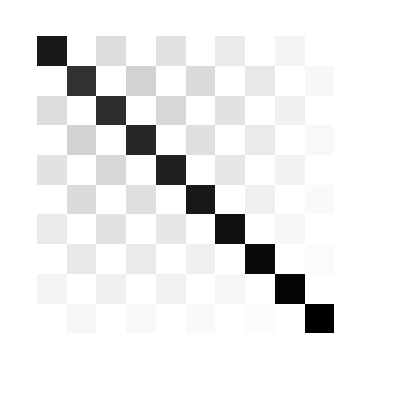

```mathematica
ArrayPlot[%32]
```